```mathematica
l0[x_]=((x-Pi/4)(x-Pi/2))/((0-Pi/4)(0-Pi/2))
```

(8 (-π/2+x) (-π/4+x))/π^2

```mathematica
l1[x_]= ((x-0)(x-Pi/2))/((Pi/4 -0)(Pi/4-Pi/2))
```

-(16 x (-π/2+x))/π^2

```mathematica
l2[x_]=((x-0)(x-Pi/4))/((Pi/2-0)(Pi/2-Pi/4))
```

(8 x (-π/4+x))/π^2

```mathematica
p[x_] = 1*l0[x] + Cos[Pi/4]*l1[x] + Cos[Pi/2]*l2[x]
```

-(8 √2 x (-π/2+x))/π^2+(8 (-π/2+x) (-π/4+x))/π^2

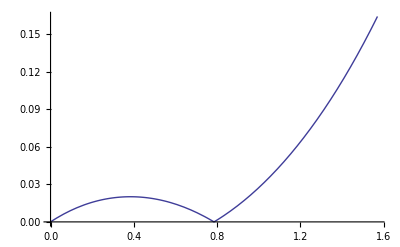

```mathematica
Plot[Abs[(Cos[x]-p[x])/Cos[x]],{x,0,Pi/2}]
```

```mathematica
(*Интерполационен полином на Ермит*)
f[x_] = Cos[x]
g[x_] = 1 - 4x^2/Pi^2
```

Cos[x]

1-(4 x^2)/π^2

```mathematica
(*Графика на относителната грешка по абсолютна стойност*)
```

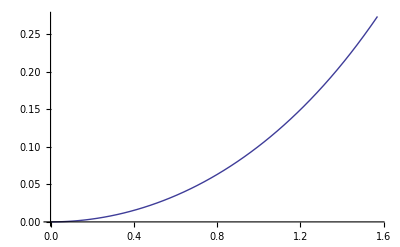

```mathematica
Plot[Abs[(f[x]-g[x])/f[x]], {x,0,Pi/2}]
```